```mathematica
(* Functions *)

equilPopSize[T_,b_,di_]:=Module[{yEq,Ne},
yEq=y/.FindRoot[(di-1)==(1-y)(1-Exp[-b y]),{y,0.9}][[1]];
Ne = yEq*T;
Ne
];
(* Mutant progeny of progenitor *)
pMutWin[T_,b_,sa_,cr_,Ne_]:=Module[{Ue,Lwt,Lmt,pWin},
(* If mutant is due to mutation in abs fit trait, use cr=0 *)
(* If mutant is due to mutation in rel fit trait, use cr>0 *)

(* Unoccupied territories *)
Ue = Round[T-Ne];
 (* Juvenile density *) 
Lwt = b (Ne-1)/T;
(* Mutant juvenile density *)
Lmt = b/T; 

(* Expected probability of winning one territory *)
pWin = Sum[  (i(1+cr))/(i(1+cr)+j)*PDF[PoissonDistribution[Lmt],i] *PDF[PoissonDistribution[Lwt],j] ,{i,1,100},{j,0,100}];
pWin
];

pMutWinTerritories[T_,b_,di_,sa_,cr_,Ne_,pWin_,k_]:=Module[{ProbWinKTerritories,Ue},
Ue =  Round[T-Ne];
ProbWinKTerritories = PDF[BinomialDistribution[Ue,pWin],k];
ProbWinKTerritories
];

(* pfix for 1 Mut juvenile surviving to adult phase *)
pSurvPhaseI[T_,b_,di_,sa_,cr_]:=Module[{Ne,Ue,Lwt,Lmt,pWin},
(* If mutant is due to mutation in abs fit trait, use cr=0 *)
(* If mutant is due to mutation in rel fit trait, use cr>0 *)
Ne=equilPopSize[T,b,di]; (* Equilibrium population size *)
Ue =  Round[T-Ne];
Lwt = b Ne/T; (* Juvenile density *)

pWin = (1/di)(Ue/T) (Sum[  (1+cr)/((1+cr)+j) *PDF[PoissonDistribution[Lwt],j] ,{j,0,Round[1000*Lwt]}]);
pWin
];

(* estimated pfix for 1 mut adult *)
pFixPhaseII[T_,b_,di_,sa_,cr_,maxSum_]:=Module[{Ne,pWin,p10,p11,p12,pExt,pFix},
(* If mutant is due to mutation in abs fit trait, use cr=0 *)
(* If mutant is due to mutation in rel fit trait, use cr>0 *)

 (* Equilibrium population size *)
Ne=equilPopSize[T,b,di];
pWin =pMutWin[T,b,sa,cr,Ne];

(*calculate transition probabilities *) (* no relative advantage with sa as there is no "progress" mutant wise *)
p10=Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],0],{k,0,maxSum}];
p11 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],1],{k,0,maxSum}];
p12 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],2],{k,1,maxSum}]; (* At least one offspring needed*)

(* estimate pfix of one reproducing mut adult *)
pExt = pe/.FindRoot[pe == p10+p11 pe + p12 pe^2,{pe,0.0}][[1]];
pFix = 1-pExt;
pFix
];
```

```mathematica
(* Parameter *)
T = 10^9;
b = 1.5;
di=3.0; (* d < b+1 for eq pop*)

sa=0.00;
cr=0.02;
maxSum=1000;

Ne=equilPopSize[T,b,di]
pWin =pMutWin[T,b,sa,cr,Ne]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

4.18239×10^8

1.11752×10^-9

```mathematica
pFixPhaseII[T,b,di,sa,cr,maxSum]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0904691

```mathematica
Ne=equilPopSize[T,b,di]
pWin =pMutWin[T,b,sa,cr,Ne]
```

6.89749×10^8

9.39056×10^-10

```mathematica
(*calculate transition probabilities *)
(* Parameter *)
T = 10^9;
b = 1.5;
di=3.0; (* d < b+1 for eq pop*)

sa=0.00;
cr=0.02;
maxSum=1000;
p10=Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],0],{k,0,maxSum}];
p11 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],1],{k,0,maxSum}];
p12 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],2],{k,1,maxSum}];
p13 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],3],{k,2,maxSum}];
p14 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],4],{k,3,maxSum}];
p15 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],5],{k,4,maxSum}];

p11210 = Join[{p10,p11},Table[ Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],n],{k,n-1,maxSum}],{n,2,10}]];



{p10,p10+p11,p10+p11+p12,p10+p11+p12+p13,p10+p11+p12+p13+p14, p10+p11+p12+p13+p14 + p15};
```

```mathematica
mu1 = Sum[k(p11210[[k]]),{k,1,Length[p11210]}]
sig1 = Sum[(k-mu1)^2(p11210[[k]]),{k,1,Length[p11210]}]
mu1/sig1
```

1.55004

0.438932

3.5314

```mathematica
mu1/sig1
```

```mathematica
p14 = Sum[pMutWinTerritories[T,b,di,sa,cr,Ne,pWin,k]*PDF[BinomialDistribution[k+1,(1/di)],4],{k,3,maxSum}]
```

0.99727

0.00273043

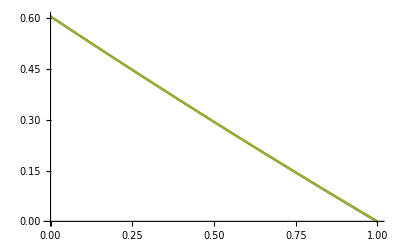

```mathematica
(* estimate pfix of one reproducing mut adult *)
pExt = pe/.FindRoot[pe == p10+p11 pe + p12 pe^2,{pe,0.0}][[1]]
pFix = 1-pExt;
pFix
Plot[ {p10+(p11 -1)pe + p12 pe^2,p10+(p11 -1)pe + p12 pe^2+p13 pe^3+p14 pe^4,p10+(p11 -1)pe + p12 pe^2+p13 pe^3+p14 pe^4+p15 pe^5},{pe,0,1}]
```

```mathematica
Log[(100/98)/di]/Log[1+0.02]
```

-33.9826